-Graphics-

Narcissistic Numbers

Students

Baskaya, Semi Kaan, Student-ID, s_baskaya23@stud.hwr-berlin.de

Busson, Jan, Student-ID, s_busson23@stud.hwr-berlin.de

Haaken, Jan, Student-ID, xxx.xxx@xxx.de

Lecture		Optimization and Data Analytics

Lecturer		Prof. Dr. Frank Brand

## Content Overview

Statutory Declaration

1 Executive Summary     xx

2 Introduction     xx

3 Problem Statement     xx

4 Solution     xx

4.1 xxx     xx

4.2 xxx     xx

4.3 xxx     xx

5 Sensitivity Analysis     xx

5.1 xxx     xx

5.2 xxx     xx

5.3 xxx     xx

6 Possible Generalizations of the Problem     xx

6.1 xxx     xx

6.2 xxx     xx

6.3 xxx     xx

7 Consequences and Recommendations     xx

8 Summary of results     xx

## Statutory Declaration

I hereby formally declare that we have written the submitted term paper entirely by ourselves without anyone else’s assistance. Wherever we have drawn on literature or other sources, either in direct quotes or in paraphrasing such material, we have given the reference to the original author or authors and to the source where it appeared. We are aware that the use of quotations, or close paraphrasing, from books, magazines, newspapers, the internet, or other sources, which are not marked as such, will be considered an attempt at deception, and that the term paper will be graded with a fail. We are aware of the fact, that the use of Large Language Models (LLM) like ChatGPT or others without a quotation will be graded with a fail, too.

____________________

Location / Date

___________________________

Signature

___________________________

Signature

___________________________

Signature

## 1 Executive Summary

Narcissistic numbers (or Armstrong number) are numbers that can be recreated by summing each of their digits raised to the power of the total number of digits in the number itself. For example, the number 153 is a narcissistic number because it has three digits and satisfies the equation:

153 = 1^3+5^3+3^3

The objective of this project is to find as many narcissistic numbers as possible. A major challenge is the rapidly increasing runtime required to test larger numbers. A pure brute force approach checks every number individually by calculating the sum of its powered digits and comparing the result with the original number. However, the search space grows exponentially with the number of digits.

For example if checking a single number requires only 1 microsecond (10^-6 seconds) testing all numbers up to:
(10^6) numbers would already take about 1 second, (10^9) numbers would take about 17 minutes, (10^12) numbers would require around 11.5 days, and (10^15) numbers would take more than 31 years.

Because of this exponential growth, the main task of this project is to develop an optimized algorithm and strategies that minimize runtime as much as possible. The more efficient the approach is, the more narcissistic numbers can realistically be found within a limited amount of computation time.

## 2 Introduction

This Mathematica notebook documents the project “Narcissistic Numbers”. The project was completed as part of the course Optimization and Simulation during the Summer Semester 2026.

## 3 Problem Statement

Narcissistic numbers, also known as Armstrong numbers, are a special subset of natural numbers. An n-digit number is defined as narcissistic if the sum of its digits, each raised to the power of n, is equal to the number itself.

A well known example of a three digit narcissistic number (n = 3) is: 153 = 1^3+5^3+3^3 (Note: 153 = 1 + 125 + 27)

In 1985, D. Winter mathematically proved that within the base 10 numeral system, narcissistic numbers can only exist up to a maximum length of 60 digits. This upper bound is derived from the following inequality constraint [1]: n*9^n < 10^(n-1)

For any dimension greater than 60, the maximum possible sum of the powered digits (n*9^n) is strictly less than the smallest possible number of that length (10^(n-1)), making the existence of larger narcissistic numbers mathematically impossible. Consequently, there are exactly 88 narcissistic numbers in base 10, with the largest being the 39 digit number:

115,132,219,018,763,992,565,095,597,973,971,522,401

The primary objective of this term paper is to develop and implement the most efficient algorithmic approach to search for and identify as many of these 88 narcissistic numbers as computationally feasible.

## 4 Solution

The following parameters define the dimension up to which an approach runs. They can be configured to test and compare the performance and speed of the different approaches presented in this notebook.

```mathematica
maxdimension = 11;
```

The first step is to define a function that can check whether any given number is narcissistic. For this purpose, a quality function QF is defined.

```mathematica
F[n_]:=Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}]
```

The quality function is derived by subtracting the digit power sum of a number from the number itself. Squaring this ensures that the function yields only positive values. Now narcissistic numbers represent not only the roots (zero) but also the global minima of the quality function.

In optimization theory, this squared approach acts like a quadratic penalty function. The squaring mechanism penalizes larger deviations from the target value.

```mathematica
QF[n_]:=(n-Sum[IntegerDigits[n][[i]]^IntegerLength[n],{i,1,IntegerLength[n]}])^2
```

For all narcissistic numbers: QF(n) = 0

```mathematica
QF[153]
```

0

For all non narcissistic numbers: QF(n) ≠ 0

```mathematica
QF[152]
```

324

The figure shows the values of the quality function QF(n) for integers 0 ≤ n ≤ 25.The zeros of the graph identify all narcissistic numbers in the considered range. Since every single digit number is equal to the sum of its digits raised to the first power, the numbers 0-9 appear as zeros of the function. Values close to zero indicate numbers that nearly satisfy the narcissistic condition.

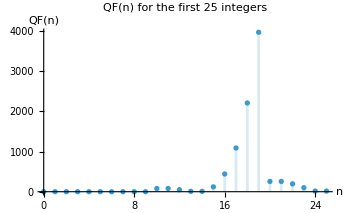

```mathematica
Show[DiscretePlot[QF[n],{n,0,25},AxesLabel->{"n","QF(n)"},PlotLabel->"QF(n) for the first 25 integers"],PlotRange->Full]
```

The following function returns all narcissistic numbers in an interval and  the time required for the calculation.

```mathematica
returnNarcissisticRange[lower_,upper_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[Select[Range[lower,upper],QF[#]==0&]];
{numbers,time}]
```

### 4.1 Brute force

Brute force describes an algorithmic approach in which all possible candidates are tested until a solution is found. Since this method does not use any filtering or optimization strategies, it is computationally more expensive than more advanced algorithms.

In this case, the brute force approach checks every number within the given range. For each number, the quality function is evaluated in order to determine whether the number is narcissistic or not.

Source: https://dl.acm.org/doi/10.1145/3107239, accessed June 16, 2026.

The following table shows the narcissistic numbers found within each power-of-10 range, together with the corresponding computation time.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

$Aborted

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[rows,{Upper bound,Numbers,Time in seconds}].

Grid[Prepend[rows,{Upper bound,Numbers,Time in seconds}],Frame→All]

The table shows that the brute force approach becomes inefficient as the search range increases, because every number in the range is checked individually. Nevertheless, it remains useful as a simple baseline for validating later approaches. However, it is not suitable as a final solution for this problem, so a more optimized approach is required.

### 4.2 Brute force parallelized

The brute force approach can be improved by parallelizing the evaluation of the candidate numbers. Since the quality function can be applied to each number independently, the search range is distributed across multiple Mathematica subkernels using ParallelTable. Each candidate number is tested by evaluating QF[n], and numbers with QF[n] = 0 are identified as narcissistic numbers.

Although this reduces the computation time, the algorithm still checks every number in the given range. Therefore, the parallelized brute force approach improves practical runtime but does not solve the scalability problem of the original brute force method.

The following table shows the narcissistic numbers found up to each upper bound and the corresponding computation time of the parallelized brute force implementation.

```mathematica
LaunchKernels[];

DistributeDefinitions[F,QF];

returnNarcissisticParallel[n_]:=Module[{time,numbers},{time,numbers}=AbsoluteTiming[ParallelTable[If[QF[i]==0,i,Nothing],{i,0,n},Method->"CoarsestGrained"]];
{numbers,time}]
```

```mathematica
rows=Table[{numbers,time}=returnNarcissisticParallel[10^k];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,3}]},{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper Bound","Numbers","Time in seconds"}],Frame->All]
```

$Aborted

Prepend::normal: Nonatomic expression expected at position 1 in Prepend[rows,{Upper Bound,Numbers,Time in seconds}].

Grid[Prepend[rows,{Upper Bound,Numbers,Time in seconds}],Frame→All]

```mathematica
CloseKernels[]
```

{Local,Local,Local,Local,Local,Local}

The results show that parallelization significantly improves the runtime compared to the sequential brute force approach. Since the evaluation of each candidate number is independent, the workload can be distributed effectively across multiple Mathematica subkernels.

However, the underlying algorithmic structure remains unchanged. Even in the parallelized version, every number in the search range is still checked individually. Therefore, parallelization reduces the practical computation time, but it does not remove the fundamental scalability limitation of the brute force method.

### 4.3 Digit Permutation Class Approach

A limitation of the brute force approach is that it checks numbers individually, even if several numbers consist of the same digits in a different order. For example, the numbers 153, 315 and 531 have the same digit composition. Since the power sum only depends on the digits and not on their order, all numbers within the same digit permutation class have the same power sum.

However, this does not mean that all permutations are narcissistic numbers. The computed power sum is the same for each permutation, but only the number that is equal to this sum can be narcissistic. In this example, the power sum is 153, so 153 is narcissistic, while its other permutations are not.

This observation suggests that the calculation can be improved by grouping numbers with the same digit composition. Instead of recomputing the power sum for every single permutation, each digit composition only has to be evaluated once.

In the following, this optimization is referred to as the digit permutation class approach.

To avoid recalculating the same digit composition multiple times, each number is first represented by its digit vector. This vector stores how often each digit from 0 to 9 occurs in the number.

```mathematica
digitVector[n_]:=Table[Count[IntegerDigits[n],d],{d,0,9}]
```

Based on this digit vector, the narcissistic sum can be calculated once for the whole permutation class. All numbers with the same digit vector produce the same sum.

```mathematica
digitVectorsOfLength[digits_]:=FrobeniusSolve[ConstantArray[1,10],digits]
permutationClassVectorPowerSum[v_]:=Module[{digits},digits=Total[v];
Sum[v[[d+1]]*d^digits,{d,0,9}]]
```

The main function first determines the relevant digit lengths for the selected range. It then generates all possible digit vectors for these lengths. For each digit vector, the corresponding power sum is calculated. This value is the only possible candidate that could be narcissistic for this digit composition. Finally, the candidate is checked by comparing its digit vector with the original digit vector and by verifying that it lies within the selected range.

```mathematica
returnNarcissisticPermutationRange[lower_,upper_]:=Module[{time,numbers,minDigits,maxDigits,vectors},minDigits=Max[1,IntegerLength[lower]];
maxDigits=IntegerLength[upper];
{time,numbers}=AbsoluteTiming[vectors=Join@@Table[digitVectorsOfLength[d],{d,minDigits,maxDigits}];
numbers=Table[Module[{value},value=permutationClassVectorPowerSum[v];
If[lower<=value<=upper&&digitVector[value]==v,value,Nothing]],{v,vectors}];
Sort[DeleteDuplicates[numbers]]];
{numbers,time}]
```

The following table applies the digit permutation class approach to increasing upper bounds. For each upper bound, the table shows the narcissistic numbers found in the corresponding range and the computation time required.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRange[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.001071
10^1 | ; ; 23456789 | 0.003731
10^2 | ; ;  | 0.013459
10^3 | ; ; 153370371407 | 0.046858
10^4 | ; ; 163482089474 | 0.088494
10^5 | ; ; 547489272793084 | 0.205735
10^6 | ; ; 548834 | 0.554943
10^7 | ; ; 1741725421081898008179926315 | 1.169670
10^8 | ; ; 246780502467805188593477 | 2.247214
10^9 | ; ; 146511208472335975534494836912985153 | 4.242460
10^10 | ; ; 4679307774 | 8.956583
10^11 | ; ; 3216404965032164049651400283942254267829060344708635679493885506068269391657894204591914 | 15.014914

The results show a clear improvement compared to the basic brute force approach. By evaluating each digit composition only once, redundant calculations for numbers with the same digits in a different order are avoided. This significantly reduces the computation time and allows larger search ranges to be tested more efficiently.

However, the approach still depends on the number of possible digit compositions, which also increases for larger dimensions. Therefore, the digit permutation class approach improves the brute force method, but further optimization is still required for very large search spaces.

### 4.4 Digit Permutation Class Approach parallelized

The digit permutation class approach already reduces redundant calculations by evaluating each digit composition only once. However, the remaining digit compositions still have to be processed one after another in the basic implementation.

A further optimization is to parallelize this process. Since each digit composition can be evaluated independently, the workload can be distributed across multiple processor cores. This means that several digit classes are checked at the same time instead of being processed sequentially.

```mathematica
LaunchKernels[];

DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum]
```

{}

```mathematica
returnNarcissisticPermutationRangeParallel[lower_,upper_]:=Module[{time,numbers,minDigits,maxDigits,vectors},If[$KernelCount==0,LaunchKernels[]];
DistributeDefinitions[digitVector,digitVectorsOfLength,permutationClassVectorPowerSum];
minDigits=Max[1,IntegerLength[lower]];
maxDigits=IntegerLength[upper];
{time,numbers}=AbsoluteTiming[vectors=Join@@Table[digitVectorsOfLength[d],{d,minDigits,maxDigits}];
numbers=ParallelTable[Module[{value},value=permutationClassVectorPowerSum[v];
If[lower<=value<=upper&&digitVector[value]==v,value,Nothing]],{v,vectors}];
Sort[DeleteDuplicates[numbers]]];
{numbers,time}]
```

The following table applies the parallelized digit permutation class approach to increasing upper bounds. For each upper bound, the table shows the narcissistic numbers found in the corresponding range and the computation time required.

```mathematica
rows=Table[Module[{lower,upper,numbers,time},upper=10^k;
lower=If[k==0,0,10^(k-1)+1];
{numbers,time}=returnNarcissisticPermutationRangeParallel[lower,upper];
{Superscript[10,k],Row[numbers,"; "],NumberForm[time,{Infinity,6}]}],{k,0,maxdimension}];

Grid[Prepend[rows,{"Upper bound","Numbers","Time in seconds"}],Frame->All]
```

Upper bound | Numbers | Time in seconds
10^0 | ; ; 01 | 0.016647
10^1 | ; ; 23456789 | 0.021302
10^2 | ; ;  | 0.037645
10^3 | ; ; 153370371407 | 0.051882
10^4 | ; ; 163482089474 | 0.099262
10^5 | ; ; 547489272793084 | 0.235507
10^6 | ; ; 548834 | 0.632848
10^7 | ; ; 1741725421081898008179926315 | 1.351001
10^8 | ; ; 246780502467805188593477 | 2.798549
10^9 | ; ; 146511208472335975534494836912985153 | 4.685153
10^10 | ; ; 4679307774 | 8.474756
10^11 | ; ; 3216404965032164049651400283942254267829060344708635679493885506068269391657894204591914 | 15.256916

The results show that parallelization does not automatically lead to faster runtimes for small search ranges. This is because starting kernels, distributing definitions, and coordinating parallel tasks introduces additional overhead. For larger ranges, however, the workload becomes large enough for parallelization to be beneficial. In these cases, the parallelized digit permutation class approach reduces the computation time compared to the non-parallel version.

Overall, this approach combines the main advantage of the digit permutation class method with parallel execution. It avoids redundant calculations between permutations and processes the remaining digit compositions more efficiently.

## 5 Sensitivity Analysis

The previous chapter introduced several algorithmic approaches for identifying narcissistic numbers. These approaches differ in how they handle the search space and how much redundant computation they avoid. However, runtime performance is not only determined by the algorithm itself, but also by input size, digit length, implementation details, and the use of parallelization.

The purpose of this sensitivity analysis is therefore to examine how strongly the computation time reacts to changes in selected parameters. In this notebook, the most relevant parameter is the digit dimension of the search interval. Increasing the number of digits directly increases the number of candidate numbers in the brute force approach. In contrast, the digit permutation class approach reacts differently, because it operates on digit compositions instead of individual numbers.

Furthermore, the sensitivity analysis investigates whether parallelization consistently improves runtime. Since parallelization introduces overhead through kernel startup, task distribution, and result collection, it is not guaranteed to be faster for small search spaces. The analysis therefore helps to identify under which conditions each approach becomes efficient.

### 5.1 Sensitivity to Search Dimensions

The first sensitivity parameter is the digit length of the search interval. This parameter has a direct effect on the size of the search space. In the brute force approach, every number in the interval has to be checked individually. Therefore, the number of candidates grows exponentially with the digit length.

For a fixed digit length d, there are 9 * 10^(d - 1) positive d-digit numbers. This explains why the brute force approach quickly becomes infeasible for larger dimensions.

The digit permutation class approach is less sensitive to the raw number of candidates. Instead of evaluating every number, it evaluates possible digit compositions. The number of digit compositions of length d corresponds to the number of non-negative integer solutions of x0 + x1 + ... + x9 = d, which is Binomial[d + 9, 9]. Although this number also increases, it grows much more slowly than the full brute force search space.

```mathematica
Clear[candidateCount,digitClassCount]

candidateCount[d_]:=If[d==1,10,9*10^(d-1)]

digitClassCount[d_]:=Binomial[d+9,9]

complexityRows=Table[{d,candidateCount[d],digitClassCount[d],NumberForm[N[candidateCount[d]/digitClassCount[d]],{Infinity,2}]},{d,1,maxdimension}];

Grid[Prepend[complexityRows,{"Digit length","Brute force candidates","Digit classes","Reduction factor"}],Frame->All]
```

Digit length | Brute force candidates | Digit classes | Reduction factor
1 | 10 | 10 | 1.00
2 | 90 | 55 | 1.64
3 | 900 | 220 | 4.09
4 | 9000 | 715 | 12.59
5 | 90000 | 2002 | 44.96
6 | 900000 | 5005 | 179.82
7 | 9000000 | 11440 | 786.71
8 | 90000000 | 24310 | 3702.18
9 | 900000000 | 48620 | 18510.90
10 | 9000000000 | 92378 | 97425.79
11 | 90000000000 | 167960 | 535841.87

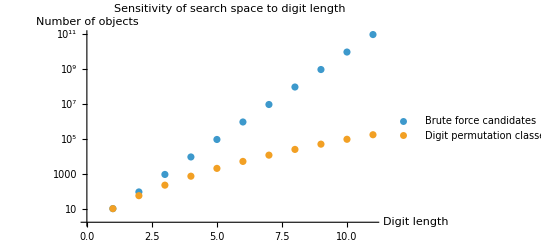

```mathematica
ListLogPlot[{Table[{d,candidateCount[d]},{d,1,maxdimension}],Table[{d,digitClassCount[d]},{d,1,maxdimension}]},PlotLegends->{"Brute force candidates","Digit permutation classes"},AxesLabel->{"Digit length","Number of objects"},PlotLabel->"Sensitivity of search space to digit length"]
```

### 5.2 Sensitivity to Algorithmic Approach

The second sensitivity analysis compares the runtime behavior of the different algorithmic approaches. To make the comparison fair, all approaches are applied to the same digit intervals. This means that for each digit length d, only numbers with exactly d digits are considered.

This avoids repeatedly recalculating smaller numbers and allows the marginal runtime increase per digit dimension to be observed more clearly. The comparison shows how sensitive each algorithm is to an increase in the size of the search space.

The expectation is that the brute force methods will show the strongest runtime increase, because they process every candidate number individually. The digit permutation class approaches should be less sensitive to the digit length, since they operate on digit vectors instead of individual numbers.

```mathematica
Clear[measureRuntime,formatRuntimeRow]

measureRuntime[name_,func_,d_Integer,repetitions_:3,timeLimit_:120]:=Module[{lower,upper,runs,successfulRuns,times,nums,t},{lower,upper}=dimensionRange[d];
runs=Table[TimeConstrained[{nums,t}=func[lower,upper];
{nums,t},timeLimit,$Failed],{repetitions}];
successfulRuns=DeleteCases[runs,$Failed];
If[successfulRuns==={},{name,d,lower,upper,0,Missing["Timeout"],Missing["NotAvailable"],Missing["NotAvailable"]},times=successfulRuns[[All,2]];
{name,d,lower,upper,Length[successfulRuns],Mean[times],If[Length[times]>1,StandardDeviation[times],0],Length[First[successfulRuns][[1]]]}]]

formatRuntimeRow[row_]:=Module[{name,d,lower,upper,completed,mean,sd,found},{name,d,lower,upper,completed,mean,sd,found}=row;
{name,d,Row[{lower," - ",upper}],completed,If[Head[mean]===Missing,"timeout",NumberForm[mean,{Infinity,6}]],If[Head[sd]===Missing,"-",NumberForm[sd,{Infinity,6}]],If[Head[found]===Missing,"-",found]}]
```

```mathematica
settings={{"Brute force",returnNarcissisticRange,Range[1,6]},{"Parallel brute force",returnNarcissisticParallelRange,Range[1,7]},{"Digit permutation class",returnNarcissisticPermutationRange,Range[1,maxdimension]},{"Parallel digit permutation class",returnNarcissisticPermutationRangeParallel,Range[1,maxdimension]}};

repetitions=3;

runtimeRows=Flatten[Table[Table[measureRuntime[setting[[1]],setting[[2]],d,repetitions,120],{d,setting[[3]]}],{setting,settings}],1];

Grid[Prepend[formatRuntimeRow/@runtimeRows,{"Method","Digits","Range","Completed runs","Mean time","Std. dev.","Numbers found"}],Frame->All]
```

Set::shape: Lists {lower$224428,upper$224428} and dimensionRange[1] are not the same shape.

Range::range: Range specification in Range[lower$224428,upper$224428] does not have appropriate bounds.

Part::pkspec1: The expression i cannot be used as a part specification.

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

Range::range: Range specification in Range[lower$224428,upper$224428] does not have appropriate bounds.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

Range::range: Range specification in Range[lower$224428,upper$224428] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Range::argb will be suppressed during this calculation.

Set::shape: Lists {lower$224627,upper$224627} and dimensionRange[2] are not the same shape.

Set::shape: Lists {lower$224723,upper$224723} and dimensionRange[3] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Method | Digits | Range | Completed runs | Mean time | Std. dev. | Numbers found
Brute force | 1 | lower$224428 - upper$224428 | 3 | 0.340337 | 0.581351 | 0
Brute force | 2 | lower$224627 - upper$224627 | 3 | 0.033609 | 0.057662 | 0
Brute force | 3 | lower$224723 - upper$224723 | 3 | 0.029656 | 0.050814 | 0
Brute force | 4 | lower$224803 - upper$224803 | 3 | 0.028673 | 0.049058 | 0
Brute force | 5 | lower$224873 - upper$224873 | 3 | 0.026677 | 0.045631 | 0
Brute force | 6 | lower$224943 - upper$224943 | 3 | 0.026827 | 0.045898 | 0
Parallel brute force | 1 | lower$225013 - upper$225013 | 3 | t$225013 | 0 | 0
Parallel brute force | 2 | lower$225014 - upper$225014 | 3 | t$225014 | 0 | 0
Parallel brute force | 3 | lower$225015 - upper$225015 | 3 | t$225015 | 0 | 0
Parallel brute force | 4 | lower$225016 - upper$225016 | 3 | t$225016 | 0 | 0
Parallel brute force | 5 | lower$225017 - upper$225017 | 3 | t$225017 | 0 | 0
Parallel brute force | 6 | lower$225018 - upper$225018 | 3 | t$225018 | 0 | 0
Parallel brute force | 7 | lower$225019 - upper$225019 | 3 | t$225019 | 0 | 0
Digit permutation class | 1 | lower$225020 - upper$225020 | 3 | t$225020 | 0 | 0
Digit permutation class | 2 | lower$225021 - upper$225021 | 3 | t$225021 | 0 | 0
Digit permutation class | 3 | lower$225022 - upper$225022 | 3 | t$225022 | 0 | 0
Digit permutation class | 4 | lower$225023 - upper$225023 | 3 | t$225023 | 0 | 0
Digit permutation class | 5 | lower$225024 - upper$225024 | 3 | t$225024 | 0 | 0
Digit permutation class | 6 | lower$225025 - upper$225025 | 3 | t$225025 | 0 | 0
Digit permutation class | 7 | lower$225026 - upper$225026 | 3 | t$225026 | 0 | 0
Digit permutation class | 8 | lower$225027 - upper$225027 | 3 | t$225027 | 0 | 0
Digit permutation class | 9 | lower$225028 - upper$225028 | 3 | t$225028 | 0 | 0
Digit permutation class | 10 | lower$225029 - upper$225029 | 3 | t$225029 | 0 | 0
Digit permutation class | 11 | lower$225030 - upper$225030 | 3 | t$225030 | 0 | 0
Parallel digit permutation class | 1 | lower$225031 - upper$225031 | 3 | t$225031 | 0 | 0
Parallel digit permutation class | 2 | lower$225032 - upper$225032 | 3 | t$225032 | 0 | 0
Parallel digit permutation class | 3 | lower$225033 - upper$225033 | 3 | t$225033 | 0 | 0
Parallel digit permutation class | 4 | lower$225034 - upper$225034 | 3 | t$225034 | 0 | 0
Parallel digit permutation class | 5 | lower$225035 - upper$225035 | 3 | t$225035 | 0 | 0
Parallel digit permutation class | 6 | lower$225036 - upper$225036 | 3 | t$225036 | 0 | 0
Parallel digit permutation class | 7 | lower$225037 - upper$225037 | 3 | t$225037 | 0 | 0
Parallel digit permutation class | 8 | lower$225038 - upper$225038 | 3 | t$225038 | 0 | 0
Parallel digit permutation class | 9 | lower$225039 - upper$225039 | 3 | t$225039 | 0 | 0
Parallel digit permutation class | 10 | lower$225040 - upper$225040 | 3 | t$225040 | 0 | 0
Parallel digit permutation class | 11 | lower$225041 - upper$225041 | 3 | t$225041 | 0 | 0

```mathematica
runtimePlotData=Table[With[{method=settings[[i,1]]},Cases[runtimeRows,row_/;row[[1]]==method&&NumericQ[row[[6]]]:>{row[[2]],row[[6]]}]],{i,Length[settings]}];

ListLogPlot[runtimePlotData,PlotLegends->settings[[All,1]],AxesLabel->{"Digit length","Mean runtime in seconds"},PlotLabel->"Runtime sensitivity by digit length"]
```

ListLogPlot::lpn: {{{1.,-1.07782},{2.,-3.39296},{3.,-3.51809},{4.,-3.55179},{5.,-3.62397},{6.,-3.61833}},{},{},{}} is not a list of numbers or pairs of numbers.

ListLogPlot[{{{1,0.340337},{2,0.033609},{3,0.0296561},{4,0.0286734},{5,0.0266766},{6,0.0268274}},{},{},{}},PlotLegends→{Brute force,Parallel brute force,Digit permutation class,Parallel digit permutation class},AxesLabel→{Digit length,Mean runtime in seconds},PlotLabel→Runtime sensitivity by digit length]

### 5.3 Sensitivity to Paralellization

The third sensitivity parameter is the degree of parallelization. Parallel execution can reduce runtime when the workload is large enough to compensate for the overhead of managing multiple kernels. However, for small search spaces, this overhead can dominate the actual computation time.

The results indicate that parallelization is not universally beneficial. Especially for smaller digit dimensions, the non-parallel digit permutation class approach can be faster because it avoids kernel startup and communication overhead. For larger dimensions, parallelization may become more useful, but this depends on the number of available processor cores and the size of the generated digit vector list.

Therefore, the sensitivity analysis shows that parallelization should not be treated as an automatic optimization. It is only advantageous when the computational workload per parallel task is sufficiently large.

```mathematica
Clear[kernelSensitivityRows]

testDimension=10;
kernelCounts=Range[1,Min[4,$ProcessorCount]];

kernelSensitivityRows=Table[CloseKernels[];
LaunchKernels[kernels];
{numbers,time}=returnNarcissisticPermutationRangeParallel@@dimensionRange[testDimension];
{kernels,testDimension,NumberForm[time,{Infinity,6}],Length[numbers]},{kernels,kernelCounts}];

CloseKernels[];

Grid[Prepend[kernelSensitivityRows,{"Kernels","Digit length","Time in seconds","Numbers found"}],Frame->All]
```

Set::shape: Lists {numbers,time} and returnNarcissisticPermutationRangeParallel[10] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Kernels | Digit length | Time in seconds | Numbers found
1 | 10 | 375.503535 | 28
2 | 10 | 375.503535 | 28
3 | 10 | 375.503535 | 28
4 | 10 | 375.503535 | 28

## 6 Possible Generalizations of the Problem

The concept of narcissistic numbers can be extended in several ways. The following generalizations explore broader mathematical ideas related to digit powers and number representations.

### 6.1 Different Number Bases

In this project, narcissistic numbers are mainly investigated in base 10. However, the concept can be generalized to any numeral system.  

The decimal number 62_10, represented as 332_4​ in base 4, is a narcissistic number in base 4.”

Verification: 3*4^4 + 3*4^1 + 2*4^0 = 48 + 12 + 2 = 62_10

Since 332_4 consists of three digits, each digit is raised to the third power: 3^3 + 3^3 + 2^3 = 27 + 27 + 8 = 62_10

Therefore, 62_10 = 332_4 = 3^3 + 3^3 + 2^3 which proves that 62_10 is a narcissistic number in base 4.

### 6.2 Generalizations and Variants of Narcissistic Numbers

In addition to the classical definition, several related types of narcissistic numbers can be found.

Narcissistic numbers with increasing exponents: 2427 = 2^1 + 4^2+ 2^3 + 7^4 = 2 + 16 + 8 + 2401 = 2427

Narcissistic numbers with constant base: 4624 = 4^4+ 4^6 + 4^2+ 4^4 = 256 + 4096 + 16 + 256 = 4624

Factorion Numbers: 145 = 1! + 4! + 5! = 1 + 24 + 120 = 145

## 7 Consequenses and Recommendations

--- Text here ---

## 8 Summary of results

--- Text here ---